# James Lord Ender Laing CSE 477 HW #1: Font Design

{{2,13.5},{3,13.5},{3,19},{2,19}}

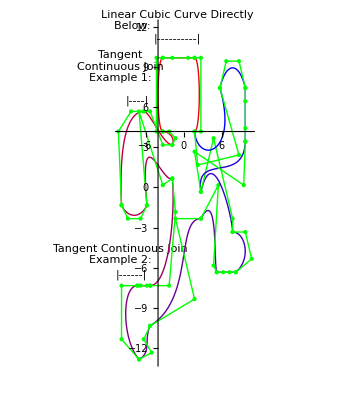

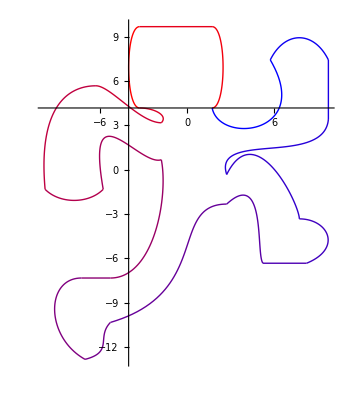

```mathematica
(*All of the 2D points making up each cubic Bezier polygon.*)
polys={
{{2,13.5},{3,13.5},{3,19},{2,19}},(*1*)
{{2,19},{1,19},{-1.5,19},{-3,19}},(*2*)
{{-3,19},{-4,19},{-4,13.5},{-3,13.5}},(*3*)
{{-3,13.5},{-2,13.5},{-1,13},{-1.5,12.5}},(*4*){{-1.5,12.5},{-3,12.5},{-5,15},{-6,15}},(*5*)
{{-6,15},{-8,15},{-10,13.5},{-9.5,8}},(*6*)
{{-9.5,8},{-8.5,7},{-6.5,7},{-5.5,8}},(*7*)
{{-5.5,8},{-6.75,15},{-3,9.5},{-1.5,10}},(*8*)
{{-1.5,10},{-1,7.5},{-2,2},{-5,2}},(*9*)
{{-5,2},{-5.5,2},{-6.5,2},{-7,2}},(*10*)
{{-7,2},{-9.5,2},{-9.5,-2},{-6.75,-3.5}},(*11*){{-6.75,-3.5},{-4.75,-3},{-6,-2},{-5,-1}},(*12*)
{{-5,-1},{2,1},{-1,7},{3,7}},(*13*)
{{3,7},{5.75,9.5},{5,3.5},{5.5,3}},(*14*)
{{5.5,3},{6.5,3},{7.5,3},{8.5,3}},(*15*)
{{8.5,3},{11,4},{10,6},{8,6}},(*16*)
{{8,6},{8,7},{5,13},{3,9}},(*17*)
{{3,9},{2,12},{9.75,9.5},{10,12.75}},(*18*){{10,12.75},{10,13.75},{10,15.75},{10,16.75}},(*19*){{10,16.75},{9,18.75},{7,18.75},{6,16.75}},(*20*)
{{6,16.75},{9,11.75},{2.5,11},{2,13.5}}(*21*)
};

(*Used for generating curves and polynomials*)
degree=4;

(*Assignment of each polygon to its own variable:*)
top=polys[[1]];
Print[top];
side=polys[[2]];
bottom=polys[[3]];
leftCurve=polys[[4]];
lowerLeftArm=polys[[5]];
upperLeftArm=polys[[6]];
leftHand=polys[[7]];
leftUnderArm=polys[[8]];
leftLeg=polys[[9]];
leftFoot=polys[[10]];
leftHeel=polys[[11]];
leftTopFoot=polys[[12]];
leftLowerLeg=polys[[13]];
rightLeg=polys[[14]];
rightFoot=polys[[15]];
rightTopFoot=polys[[16]];
rightUpperLeg=polys[[17]];
rightUnderArm=polys[[18]];
rightUpperArm=polys[[19]];
rightHand=polys[[20]];
rightTopArm=polys[[21]];

(*Each point listed out for centering purposes*)
everyPoint={{-3,19},{-1.5,19},{1,19},{2,19},{-3,16},{-4,16},{-4,19},{-3,19},{2,19},{3,19},{3,13.5},{2,13.5},{-3,13.5},{-2,13.5},{-1,13},{-1.5,12.5},{-1.5,12.5},{-3,12.5},{-5,15},{-6,15},{-6,15},{-8,15},{-10,13.5},{-9.5,8},{-9.5,8},{-8.5,7},{-6.5,7},{-5.5,8},{-5.5,8},{-6.75,15},{-3,9.5},{-1.5,10},{-1.5,10},{-1,7.5},{-2,2},{-5,2},{-5,2},{-5.5,2},{-6.5,2},{-7,2},{-7,2},{-9.5,2},{-9.5,-2},{-6.75,-3.5},{-6.75,-3.5},{-4.75,-3},{-6,-2},{-5,-1},{-5,-1},{2,1},{-1,7},{3,7},{3,7},{7,6},{5,3.5},{5.5,3},{5.5,3},{6,3},{6.5,3},{7.5,3},{7.5,3},{11,4},{10,5},{8,5.5},{8,6},{8,8},{5,10},{3,10},{3,9},{3.5,11},{7.75,10.5},{8,11.75},{10,12.75},{10,13.75},{10,15.75},{10,16.75},{10,16.75},{9,18.75},{8,18.75},{7,16.75},{6,16.75},{9,11.75},{2.5,11},{2,13.5}};

numOfPoints=Length[everyPoint];(*Used for center and distance calculations*)

(*Red and Blue are the colors I chose for the interpolation*)
firstColor=RGBColor[1,0,0];
secondColor=RGBColor[0,0,1];

(*Used to center the character around the origin*)
center=Sum[everyPoint[[i]],{i,1,numOfPoints}]/numOfPoints;
dists=Table[Norm[everyPoint[[i]]-center],{i,1,numOfPoints}];


radius=Max[dists];(*Used when plotting the character*)

(*Used for interpolation:*)
b=bottom; 
n=Length[b]-1;

(*Centers all of the points for the character:*)
Do[top[[i]]=top[[i]]-center,{i,1,degree}];
Do[side[[i]]=side[[i]]-center,{i,1,degree}];
Do[bottom[[i]]=bottom[[i]]-center,{i,1,degree}];
Do[leftCurve[[i]]=leftCurve[[i]]-center,{i,1,degree}];
Do[lowerLeftArm[[i]]=lowerLeftArm[[i]]-center,{i,1,degree}];
Do[upperLeftArm[[i]]=upperLeftArm[[i]]-center,{i,1,degree}];
Do[leftHand[[i]]=leftHand[[i]]-center,{i,1,degree}];
Do[leftUnderArm[[i]]=leftUnderArm[[i]]-center,{i,1,degree}];
Do[leftLeg[[i]]=leftLeg[[i]]-center,{i,1,degree}];
Do[leftFoot[[i]]=leftFoot[[i]]-center,{i,1,degree}];
Do[leftHeel[[i]]=leftHeel[[i]]-center,{i,1,degree}];
Do[leftTopFoot[[i]]=leftTopFoot[[i]]-center,{i,1,degree}];
Do[leftLowerLeg[[i]]=leftLowerLeg[[i]]-center,{i,1,degree}];
Do[rightLeg[[i]]=rightLeg[[i]]-center,{i,1,degree}];
Do[rightFoot[[i]]=rightFoot[[i]]-center,{i,1,degree}];
Do[rightTopFoot[[i]]=rightTopFoot[[i]]-center,{i,1,degree}];
Do[rightUpperLeg[[i]]=rightUpperLeg[[i]]-center,{i,1,degree}];
Do[rightUnderArm[[i]]=rightUnderArm[[i]]-center,{i,1,degree}];
Do[rightUpperArm[[i]]=rightUpperArm[[i]]-center,{i,1,degree}];
Do[rightHand[[i]]=rightHand[[i]]-center,{i,1,degree}];
Do[rightTopArm[[i]]=rightTopArm[[i]]-center,{i,1,degree}];

(*The Bernstein polynomials:*)
(*b30[t_]:=(1-t)^3;*)

b30[t_]=BernsteinBasis[3,0,t];
(*b31[t_]:=3*(1-t)^2*t;*)
b31[t_]=BernsteinBasis[3,1,t];
(*b32[t_]:=3*(1-t)*t^2;*)
b32[t_]=BernsteinBasis[3,2,t];
(*b33[t_]:=t^3;*)
b33[t_]=BernsteinBasis[3,3,t];
(*Alternatively,could have used BernsteinBasis[3,i,t]*)

(*Function used to generate the Bezier curve:*)
bez[b_,t_]:=b[[1]]*b30[t]+b[[2]]*b31[t]+b[[3]]*b32[t]+b[[4]]*b33[t];

(*Maps a given t-value to a 0-1 range number*)
tMap[min_,ipiece_,num_]:=(Return[(ipiece-min)/(num-min)]);

(*The function to fulfil the color interpolation requirement*)
myRGBcolor[color1_,color2_,num_,ipiece_]:=(process=tMap[1,ipiece,num];
p1=color1[[1]];
p2=color1[[2]];
p3=color1[[3]];
q1=color2[[1]];
q2=color2[[2]];
q3=color2[[3]];
n1=(1-process)*p1+process*q1;
n2=(1-process)*p2+process*q2;
n3=(1-process)*p3+process*q3;
Return[RGBColor[n1,n2,n3]];);

(*De Casteljau's Algorithm*)
dca[b_,r_,i_,t_]:=If[r==0,b[[i+1]],(1-t)*dca[b,r-1,i,t]+t*dca[b,r-1,i+1,t]];

(*Function for returning the tangent line for a given point on the character*)
tangent[curve_,numberN_,t_]:=(deriv=Table[curve[[i+1]]-curve[[i]],{i,1,numberN}];
Return[Graphics[{Thick,Arrow[{dca[curve,numberN,0,t],(dca[curve,numberN,0,t]+dca[deriv,numberN-1,0,t])}]}]]);

(*Function for generating the red dot,and updating it on the third plot*)
curvept[curve_,numberN_,t_]:=Graphics[{PointSize[Large],Red,Point[dca[curve,numberN,0,t]]}];

(*Function for mapping the t-value from plot three into terms the curvept function can understand*)
manipulateMapPoint[t_]:=(ceilingT=If[t==0,1,Ceiling[t]];
floorT=If[t==21,20,Floor[t]];
ceilingT=If[ceilingT==floorT,ceilingT+1,ceilingT];
selectedCurve=polys[[ceilingT]];
actualN=Length[selectedCurve]-1;
actualT=tMap[floorT,t,ceilingT];
Do[selectedCurve[[i]]=selectedCurve[[i]]-center,{i,1,degree}];
Return[curvept[selectedCurve,actualN,actualT]];);

(*Serves the same purpose as the previous function,but for the tangent function*)
manipulateMapTangent[t_]:=(ceilingT=If[t==0,1,Ceiling[t]];
floorT=If[t==21,20,Floor[t]];
ceilingT=If[ceilingT==floorT,ceilingT+1,ceilingT];
selectedCurve=polys[[ceilingT]];
actualN=Length[selectedCurve]-1;
actualT=tMap[floorT,t,ceilingT];
Do[selectedCurve[[i]]=selectedCurve[[i]]-center,{i,1,degree}];
Return[tangent[selectedCurve,actualN,actualT]];);

numOfParts=21; (*Used for multiple calculations*)

(*Curve calculations for each cubic Bezier Poly:*)curveplotA=ParametricPlot[bez[bottom,t],{t,0,1},PlotStyle->{Thick,myRGBcolor[firstColor,secondColor,numOfParts,1]}];
curveplotB=ParametricPlot[bez[top,t],{t,0,1},PlotStyle->{Thick,myRGBcolor[firstColor,secondColor,numOfParts,2]}];
curveplotC=ParametricPlot[bez[side,t],{t,0,1},PlotStyle->{Thick,myRGBcolor[firstColor,secondColor,numOfParts,3]}];
curveplotD=ParametricPlot[bez[leftCurve,t],{t,0,1},PlotStyle->{Thick,myRGBcolor[firstColor,secondColor,numOfParts,4]}];
curveplotE=ParametricPlot[bez[lowerLeftArm,t],{t,0,1},PlotStyle->{Thick,myRGBcolor[firstColor,secondColor,numOfParts,5]}];
curveplotF=ParametricPlot[bez[upperLeftArm,t],{t,0,1},PlotStyle->{Thick,myRGBcolor[firstColor,secondColor,numOfParts,6]}];
curveplotG=ParametricPlot[bez[leftHand,t],{t,0,1},PlotStyle->{Thick,myRGBcolor[firstColor,secondColor,numOfParts,7]}];
curveplotH=ParametricPlot[bez[leftUnderArm,t],{t,0,1},PlotStyle->{Thick,myRGBcolor[firstColor,secondColor,numOfParts,8]}];
curveplotI=ParametricPlot[bez[leftLeg,t],{t,0,1},PlotStyle->{Thick,myRGBcolor[firstColor,secondColor,numOfParts,9]}];
curveplotJ=ParametricPlot[bez[leftFoot,t],{t,0,1},PlotStyle->{Thick,myRGBcolor[firstColor,secondColor,numOfParts,10]}];
curveplotK=ParametricPlot[bez[leftHeel,t],{t,0,1},PlotStyle->{Thick,myRGBcolor[firstColor,secondColor,numOfParts,11]}];
curveplotL=ParametricPlot[bez[leftTopFoot,t],{t,0,1},PlotStyle->{Thick,myRGBcolor[firstColor,secondColor,numOfParts,12]}];
curveplotM=ParametricPlot[bez[leftLowerLeg,t],{t,0,1},PlotStyle->{Thick,myRGBcolor[firstColor,secondColor,numOfParts,13]}];
curveplotN=ParametricPlot[bez[rightLeg,t],{t,0,1},PlotStyle->{Thick,myRGBcolor[firstColor,secondColor,numOfParts,14]}];
curveplotO=ParametricPlot[bez[rightFoot,t],{t,0,1},PlotStyle->{Thick,myRGBcolor[firstColor,secondColor,numOfParts,15]}];
curveplotP=ParametricPlot[bez[rightTopFoot,t],{t,0,1},PlotStyle->{Thick,myRGBcolor[firstColor,secondColor,numOfParts,16]}];
curveplotQ=ParametricPlot[bez[rightUpperLeg,t],{t,0,1},PlotStyle->{Thick,myRGBcolor[firstColor,secondColor,numOfParts,17]}];
curveplotR=ParametricPlot[bez[rightUnderArm,t],{t,0,1},PlotStyle->{Thick,myRGBcolor[firstColor,secondColor,numOfParts,18]}];
curveplotS=ParametricPlot[bez[rightUpperArm,t],{t,0,1},PlotStyle->{Thick,myRGBcolor[firstColor,secondColor,numOfParts,19]}];
curveplotT=ParametricPlot[bez[rightHand,t],{t,0,1},PlotStyle->{Thick,myRGBcolor[firstColor,secondColor,numOfParts,20]}];
curveplotU=ParametricPlot[bez[rightTopArm,t],{t,0,1},PlotStyle->{Thick,myRGBcolor[firstColor,secondColor,numOfParts,21]}];

(*Generates Graphics objects to show each Bezier poly:*)
polygonA=Graphics[{Thick,Green,Line[bottom],Axes->True}];
polygonB=Graphics[{Thick,Green,Line[top],Axes->True}];
polygonC=Graphics[{Thick,Green,Line[side],Axes->True}];
polygonD=Graphics[{Thick,Green,Line[leftCurve],Axes->True}];
polygonE=Graphics[{Thick,Green,Line[lowerLeftArm],Axes->True}];
polygonF=Graphics[{Thick,Green,Line[upperLeftArm],Axes->True}];
polygonG=Graphics[{Thick,Green,Line[leftHand],Axes->True}];
polygonH=Graphics[{Thick,Green,Line[leftUnderArm],Axes->True}];
polygonI=Graphics[{Thick,Green,Line[leftLeg],Axes->True}];
polygonJ=Graphics[{Thick,Green,Line[leftFoot],Axes->True}];
polygonK=Graphics[{Thick,Green,Line[leftHeel],Axes->True}];
polygonL=Graphics[{Thick,Green,Line[leftTopFoot],Axes->True}];
polygonM=Graphics[{Thick,Green,Line[leftLowerLeg],Axes->True}];
polygonN=Graphics[{Thick,Green,Line[rightLeg],Axes->True}];
polygonO=Graphics[{Thick,Green,Line[rightFoot],Axes->True}];
polygonP=Graphics[{Thick,Green,Line[rightTopFoot],Axes->True}];
polygonQ=Graphics[{Thick,Green,Line[rightUpperLeg],Axes->True}];
polygonR=Graphics[{Thick,Green,Line[rightUnderArm],Axes->True}];
polygonS=Graphics[{Thick,Green,Line[rightUpperArm],Axes->True}];
polygonT=Graphics[{Thick,Green,Line[rightHand],Axes->True}];
polygonU=Graphics[{Thick,Green,Line[rightTopArm],Axes->True}];

(*Generates Graphics objects for the control points:*)
pointsA=Graphics[{PointSize[Large],Green,Point[bottom]}];
pointsB=Graphics[{PointSize[Large],Green,Point[top]}];
pointsC=Graphics[{PointSize[Large],Green,Point[side]}];
pointsD=Graphics[{PointSize[Large],Green,Point[leftCurve]}];
pointsE=Graphics[{PointSize[Large],Green,Point[lowerLeftArm]}];
pointsF=Graphics[{PointSize[Large],Green,Point[upperLeftArm]}];
pointsG=Graphics[{PointSize[Large],Green,Point[leftHand]}];
pointsH=Graphics[{PointSize[Large],Green,Point[leftUnderArm]}];
pointsI=Graphics[{PointSize[Large],Green,Point[leftLeg]}];
pointsJ=Graphics[{PointSize[Large],Green,Point[leftFoot]}];
pointsK=Graphics[{PointSize[Large],Green,Point[leftHeel]}];
pointsL=Graphics[{PointSize[Large],Green,Point[leftTopFoot]}];
pointsM=Graphics[{PointSize[Large],Green,Point[leftLowerLeg]}];
pointsN=Graphics[{PointSize[Large],Green,Point[rightLeg]}];
pointsO=Graphics[{PointSize[Large],Green,Point[rightFoot]}];
pointsP=Graphics[{PointSize[Large],Green,Point[rightTopFoot]}];
pointsQ=Graphics[{PointSize[Large],Green,Point[rightUpperLeg]}];
pointsR=Graphics[{PointSize[Large],Green,Point[rightUnderArm]}];
pointsS=Graphics[{PointSize[Large],Green,Point[rightUpperArm]}];
pointsT=Graphics[{PointSize[Large],Green,Point[rightHand]}];
pointsU=Graphics[{PointSize[Large],Green,Point[rightTopArm]}];

(*Variables used to show the labels according to the assignment description:*)
linearLabel=Text[InsertLinebreaks["Linear Cubic Curve Directly Below:                           |----------|",32],{-1,12}];
tangentLabel1=Text[InsertLinebreaks["Tangent Continuous Join Example 1:",16],{-10,9}];
tangentIdentifier1=Text[InsertLinebreaks["|----|",16],{-7.25,6.5}];
tangentLabel2=Text[InsertLinebreaks["Tangent Continuous Join Example 2:",24],{-10,-5}];
tangentIdentifier2=Text[InsertLinebreaks["|------|",16],{-8.25,-6.5}];
flavorLabelText=Graphics[{linearLabel,tangentLabel1,tangentIdentifier1,tangentLabel2,tangentIdentifier2}];

(*Function call to show everything made for Plot #1:*)
Show[{curveplotA,pointsA,polygonA,curveplotB,pointsB,polygonB,curveplotC,pointsC,polygonC,curveplotD,pointsD,polygonD,curveplotE,pointsE,polygonE,curveplotF,pointsF,polygonF,curveplotG,pointsG,polygonG,curveplotH,pointsH,polygonH,curveplotI,pointsI,polygonI,curveplotJ,pointsJ,polygonJ,curveplotK,pointsK,polygonK,curveplotL,pointsL,polygonL,curveplotM,pointsM,polygonM,curveplotN,pointsN,polygonN,curveplotO,pointsO,polygonO,curveplotP,pointsP,polygonP,curveplotQ,pointsQ,polygonQ,curveplotR,pointsR,polygonR,curveplotS,pointsS,polygonS,curveplotT,pointsT,polygonT,curveplotU,pointsU,polygonU,flavorLabelText},PlotRange->1 radius]

(*Function call to show everything made for Plot #2:*)
Show[{curveplotA,curveplotB,curveplotC,curveplotD,curveplotE,curveplotF,curveplotG,curveplotH,curveplotI,curveplotJ,curveplotK,curveplotL,curveplotM,curveplotN,curveplotO,curveplotP,curveplotQ,curveplotR,curveplotS,curveplotT,curveplotU},PlotRange->1 radius]

(*Function call to show everything made for Plot #3:*)
Manipulate[Show[{curveplotA,pointsA,polygonA,curveplotB,pointsB,polygonB,curveplotC,pointsC,polygonC,curveplotD,pointsD,polygonD,curveplotE,pointsE,polygonE,curveplotF,pointsF,polygonF,curveplotG,pointsG,polygonG,curveplotH,pointsH,polygonH,curveplotI,pointsI,polygonI,curveplotJ,pointsJ,polygonJ,curveplotK,pointsK,polygonK,curveplotL,pointsL,polygonL,curveplotM,pointsM,polygonM,curveplotN,pointsN,polygonN,curveplotO,pointsO,polygonO,curveplotP,pointsP,polygonP,curveplotQ,pointsQ,polygonQ,curveplotR,pointsR,polygonR,curveplotS,pointsS,polygonS,curveplotT,pointsT,polygonT,curveplotU,pointsU,polygonU,manipulateMapPoint[t],manipulateMapTangent[t]},PlotRange->1 radius],{t,0,21}]
```